```mathematica
Integrate[1/η Exp[-u/η]3/η Exp[-(t-u)3/η],{u,0,t}]//FullSimplify
```

(3 ⅇ^(-(3 t)/η) (-1+ⅇ^((2 t)/η)))/(2 η)

```mathematica
Integrate[(3 ⅇ^(-(3 t)/η) (-1+ⅇ^((2 t)/η)))/(2 η),{t,0,Infinity}]
```

ConditionalExpression[1,Re[η]>0]

```mathematica
Exp[-3t]*Exp[2t]
```

ⅇ^-t

```mathematica
With[{η=0.2, t=0.4},(3 ⅇ^(-(3 t)/η) (-1+ⅇ^((2 t)/η)))/(2 η)]
```

0.996424

```mathematica
With[{η=0.2, t=0.4},3/(2η)(Exp[-t/η]-Exp[-3t/η])]
```

0.996424

```mathematica
Integrate[(3 ⅇ^(-(3 u)/η) (-1+ⅇ^((2u)/η)))/(2 η)*1/η Exp[-(t-u)/η],{u,0,t}]//FullSimplify
```

(3 ⅇ^(-(3 t)/η) (ⅇ^((2 t)/η) (2 t-η)+η))/(4 η^2)

```mathematica
1/2*((3 ⅇ^(-(3 t)/η) (ⅇ^((2 t)/η) (2 t-η)+η))/(4 η^2))+1/2*((3 ⅇ^(-(3 t)/η) (-1+ⅇ^((2 t)/η)))/(2 η))//FullSimplify
```

(ⅇ^(-(3 t)/η) (-3 η+3 ⅇ^((2 t)/η) (2 t+η)))/(8 η^2)

```mathematica
Integrate[(ⅇ^(-(3 t)/η) (-3 η+3 ⅇ^((2 t)/η) (2 t+η)))/(8 η^2),{t,0,Infinity}]
```

ConditionalExpression[1,Re[η]>0]

```mathematica
FullSimplify[With[{η=1},(ⅇ^(-(3 t)/η) (-3 η+3 ⅇ^((2 t)/η) (2 t+η)))/(8 η^2)]]
```

3/8 ⅇ^(-3 t) (-1+ⅇ^(2 t) (1+2 t))

```mathematica
Integrate[(ⅇ^(-(3 t)/η) (-3 η+3 ⅇ^((2 t)/η) (2 t+η)))/(8 η^2),{t,t0,t1}]
```

(-ⅇ^(-(3 t0)/η) η+ⅇ^(-(3 t1)/η) η-3 ⅇ^(-t1/η) (2 t1+3 η)+ⅇ^(-t0/η) (6 t0+9 η))/(8 η)

```mathematica
Integrate[(1-Exp[-θ(P+t)])*Exp[-t]/(Exp[-tk]-Exp[-tkp1]),{t,tk,tkp1}]
```

1+(ⅇ^(-(P+tk+tkp1) θ) (-ⅇ^(tk (1+θ))+ⅇ^(tkp1 (1+θ))))/((ⅇ^tk-ⅇ^tkp1) (1+θ))

```mathematica
Integrate[Exp[-t],{t,0,tkp1}]
```

1-Cosh[tkp1]+Sinh[tkp1]

```mathematica
1-Exp[tkp1]
```

1-ⅇ^tkp1

```mathematica
(*pi_k*)
```

```mathematica
Integrate[3/8Exp[-s](2s+1-Exp[-2s]),{s,t1,t2}]//FullSimplify
```

1/8 (-ⅇ^(-3 t1)+ⅇ^(-3 t2)+ⅇ^-t1 (9+6 t1)-3 ⅇ^-t2 (3+2 t2))

```mathematica
(*sigma_k*)
```

```mathematica
Integrate[Exp[-s],{s,t1,t2}]//FullSimplify
```

Cosh[t1]-Cosh[t2]-Sinh[t1]+Sinh[t2]

```mathematica
(*qkLTl*)
```

```mathematica
Integrate[qtGTs[t,s]pi[s],{t,tl1,tl2}]
```

3/4 ⅇ^(-2 s-tl1-tl2) (-1+ⅇ^(2 s)) (-ⅇ^tl1+ⅇ^tl2)

```mathematica
(*qkLTl*)
```

```mathematica
Integrate[3/4 ⅇ^(-2 s-tl1-tl2) (-1+ⅇ^(2 s)) (-ⅇ^tl1+ⅇ^tl2),{s,tk1,tk2}]//FullSimplify
```

3/8 ⅇ^(-2 tk1-2 tk2-tl1-tl2) (ⅇ^tl1-ⅇ^tl2) (-ⅇ^(2 tk1)+ⅇ^(2 tk2)+2 ⅇ^(2 (tk1+tk2)) (tk1-tk2))

```mathematica
(*qkGTl*)
```

```mathematica
Integrate[qtLTs[t,s]pi[s],{t,tl1,tl2}]
```

3/8 ⅇ^-s (-ⅇ^(-2 tl1)+ⅇ^(-2 tl2)-2 tl1+2 tl2)

```mathematica
Integrate[3/8 ⅇ^-s (-ⅇ^(-2 tl1)+ⅇ^(-2 tl2)-2 tl1+2 tl2),{s,tk1,tk2}]//FullSimplify
```

3/8 ⅇ^(-tk1-tk2-2 (tl1+tl2)) (ⅇ^tk1-ⅇ^tk2) (-ⅇ^(2 tl1)+ⅇ^(2 tl2)+2 ⅇ^(2 (tl1+tl2)) (tl1-tl2))

```mathematica
(*qkEQl*)
Integrate[qtGTs[t,s]pi[s],{t,t1,t2},{s,t1,t}]
```

1/8 ⅇ^(-3 (t1+t2)) (-ⅇ^(3 t1)+2 ⅇ^(3 t2) (-1+3 ⅇ^(2 t1))+3 ⅇ^(t1+2 t2) (1+2 ⅇ^(2 t1) (-1+t1-t2)))

```mathematica
Integrate[qtLTs[t,s]pi[s],{s,t1,t2},{t,t1,s}]
```

1/8 ⅇ^(-3 (t1+t2)) (-ⅇ^(3 t1)+2 ⅇ^(3 t2) (-1+3 ⅇ^(2 t1))+3 ⅇ^(t1+2 t2) (1+2 ⅇ^(2 t1) (-1+t1-t2)))

```mathematica
2*1/8 ⅇ^(-3 (t1+t2)) (-ⅇ^(3 t1)+2 ⅇ^(3 t2) (-1+3 ⅇ^(2 t1))+3 ⅇ^(t1+2 t2) (1+2 ⅇ^(2 t1) (-1+t1-t2)))
```

1/4 ⅇ^(-3 (t1+t2)) (-ⅇ^(3 t1)+2 ⅇ^(3 t2) (-1+3 ⅇ^(2 t1))+3 ⅇ^(t1+2 t2) (1+2 ⅇ^(2 t1) (-1+t1-t2)))

```mathematica
pi[s_]:=3/8 Exp[-s](2s+1-Exp[-2s])
```

```mathematica
qtLTs[t_,s_]:=(2(1-Exp[-2t]))/(1-Exp[-2s]+2s)
```

```mathematica
qtGTs[t_,s_]:=(2Exp[-(t-s)](1-Exp[-2s]))/(1-Exp[-2s]+2s)
```

```mathematica
sigma[t_]:=Exp[-t]
```

```mathematica
Integrate[pi[s],{s,tkp1,Infinity}]
```

1/8 ⅇ^(-3 tkp1) (-1+ⅇ^(2 tkp1) (9+6 tkp1))

```mathematica
(* qkLTl_inf *)
```

```mathematica
Integrate[qtGTs[t,s]pi[s],{s,tk1,tk2},{t, tl1, Infinity}]
```

3/8 ⅇ^-tl1 (-ⅇ^(-2 tk1)+ⅇ^(-2 tk2)-2 tk1+2 tk2)

```mathematica
Integrate[qtLTs[t,s]pi[s],{s,tk1,Infinity},{t, tl1, tl2}]
```

3/8 ⅇ^-tk1 (-ⅇ^(-2 tl1)+ⅇ^(-2 tl2)-2 tl1+2 tl2)

```mathematica
Integrate[qtLTs[t,s]pi[s],{s,tk,Infinity},{t,tk,s}]
```

1/4 ⅇ^(-3 tk) (-1+3 ⅇ^(2 tk))

```mathematica
Integrate[qtGTs[t,s]pi[s],{s,tk,Infinity},{t,s,Infinity}]
```

1/4 ⅇ^(-3 tk) (-1+3 ⅇ^(2 tk))

```mathematica
1/4 ⅇ^(-3 tk) (-1+3 ⅇ^(2 tk))+1/4 ⅇ^(-3 tk) (-1+3 ⅇ^(2 tk))
```

1/2 ⅇ^(-3 tk) (-1+3 ⅇ^(2 tk))

```mathematica
lambda[s_]:=1/4(1-Exp[-2s]+2s)
```

```mathematica
σ[s_]:=Exp[-s]
```

```mathematica
(* pkLTl *)
```

```mathematica
Integrate[(1-ⅇ^(-1/4 r (1-ⅇ^(-2 s)+2 s)))qtGTs[t,s]σ[s],{s,tk1,tk2},{t,tl1,tl2}]
```

∫_tk1^tk2 (2 ⅇ^(-tl1-tl2) (-1+ⅇ^(1/4 r (-1+ⅇ^(-2 s)-2 s))) (-1+ⅇ^(2 s)) (ⅇ^tl1-ⅇ^tl2))/(-1+ⅇ^(2 s) (1+2 s))ⅆs

```mathematica
1-Exp[-lambda[s]r]
```

```mathematica
1-ⅇ^(-1/4 r (1-ⅇ^(-2 s)+2 s))
```

```mathematica
With[{r=1},NIntegrate[(1-ⅇ^(-1/4 r (1-ⅇ^(-2 s)+2 s)))qtGTs[t,s]σ[s],{s,0.2,0.8},{t,0.9,2.0}]]
```

0.0404263

```mathematica
qtGTs[t,s]
```

(2 ⅇ^(s-t) (1-ⅇ^(-2 s)))/(1-ⅇ^(-2 s)+2 s)

```mathematica
qtLTs[t,s]
```

(2 (1-ⅇ^(-2 t)))/(1-ⅇ^(-2 s)+2 s)

```mathematica
(* Mutation prob *)
```

```mathematica
Integrate[(1-Exp[-θ(s+P)])Exp[-s],{s,tk1,tk2}]//FullSimplify
```

(ⅇ^(-P θ) (-ⅇ^(-tk1 (1+θ))+ⅇ^(-tk2 (1+θ))))/(1+θ)+Cosh[tk1]-Cosh[tk2]-Sinh[tk1]+Sinh[tk2]

```mathematica
TrigToExp[(ⅇ^(-P θ) (-ⅇ^(-tk1 (1+θ))+ⅇ^(-tk2 (1+θ))))/(1+θ)+Cosh[tk1]-Cosh[tk2]-Sinh[tk1]+Sinh[tk2]]//Simplify
```

ⅇ^-tk1-ⅇ^-tk2-ⅇ^(-P θ-tk1 (1+θ))/(1+θ)+ⅇ^(-P θ-tk2 (1+θ))/(1+θ)

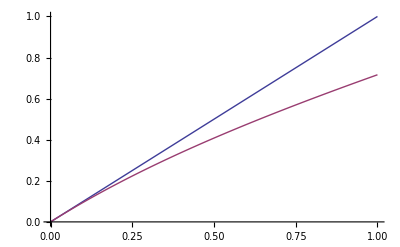

```mathematica
Plot[{s,1./4.*(1.-Exp[-2.*s]+2.*s)},{s,0,1}]
```